(0.3 | -1.10525
0.348 | -1.07996
0.396 | -1.1225
0.444 | -1.05986
0.492 | -1.06783
0.54 | -0.978257
0.588 | -0.955469
0.636 | -0.846209
0.684 | -0.794931
0.732 | -0.671395
0.78 | -0.593028
0.828 | -0.459459
0.876 | -0.354877
0.924 | -0.214726
0.972 | -0.0844691
1.02 | 0.0593841
1.068 | 0.215
1.116 | 0.360097
1.164 | 0.540909
1.212 | 0.685119
1.26 | 0.891074
1.308 | 1.03252
1.356 | 1.26364
1.404 | 1.40065
1.452 | 1.65703
1.5 | 1.7881)

-7.5242×10^10+2.57713×10^12 x-4.18831×10^13 x^2+4.29994×10^14 x^3-3.13218×10^15 x^4+1.72357×10^16 x^5-7.44836×10^16 x^6+2.59412×10^17 x^7-7.4143×10^17 x^8+1.76156×10^18 x^9-3.51121×10^18 x^10+5.90894×10^18 x^11-8.42983×10^18 x^12+1.0216×10^19 x^13-1.05192×10^19 x^14+9.18762×10^18 x^15-6.78205×10^18 x^16+4.20603×10^18 x^17-2.17233×10^18 x^18+9.22789×10^17 x^19-3.16758×10^17 x^20+8.56503×10^16 x^21-1.75563×10^16 x^22+2.56319×10^15 x^23-2.37415×10^14 x^24+1.04833×10^13 x^25

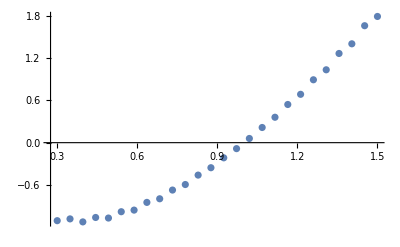

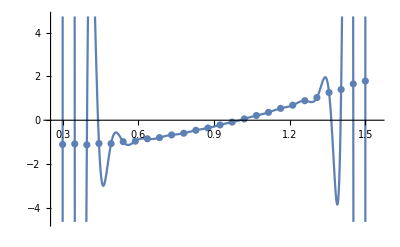

InterpolatingFunction[…]

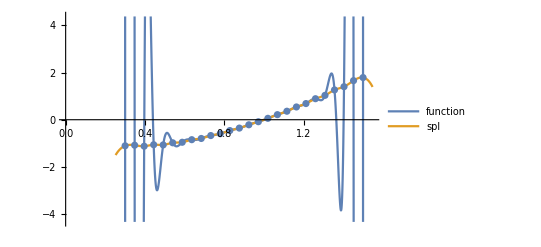

```mathematica
arr1={0.3, 0.348,0.396,0.444, 0.492, 0.54, 0.588, 0.636, 0.684, 0.732,0.78, 0.828, 0.876, 0.924, 0.972, 1.02,1.068,1.116,1.164,1.212,1.26,1.308,1.356,1.404,1.452,1.5};
arr2={-1.10525, -1.07996, -1.1225,-1.05986,-1.06783,-0.978257,-0.955469,-0.846209,-0.794931,-0.671395,-0.593028,-0.459459,-0.354877,-0.214726,-0.0844691,0.0593841,0.215,0.360097,0.540909,0.685119,0.891074,1.03252,1.26364,1.40065,1.65703,1.7881};
n=Length[arr1];funk={};
For[i=1,i≤n,i++,funk=Append[funk,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk]
inpln:=InterpolatingPolynomial[funk,x];Collect[inpln,x]
ListPlot[funk]
gr1:=Plot[inpln,{x,0.252,1.548}];
gr2:=ListPlot[funk];
Show[{gr1,gr2}]
sp=Interpolation[funk,Method->"Spline"]
gr3:=Plot[{inpln,sp[x]},{x,0.252,1.548},{PlotLegends->{"function", "spl"},AxesOrigin->{0,0}}];
gr2:=ListPlot[funk];
Show[{gr3,gr2}]
```

(0.3 | -1.10525
0.396 | -1.1225
0.492 | -1.06783
0.588 | -0.955469
0.684 | -0.794931
0.78 | -0.593028
0.876 | -0.354877
0.972 | -0.0844691
1.068 | 0.215
1.164 | 0.540909
1.26 | 0.891074
1.356 | 1.26364
1.452 | 1.65703)

-0.0289269-9.84676 x+43.7942 x^2-146.623 x^3+388.573 x^4-758.571 x^5+1084.2 x^6-1130.47 x^7+849.518 x^8-447.827 x^9+157.075 x^10-32.9087 x^11+3.11494 x^12

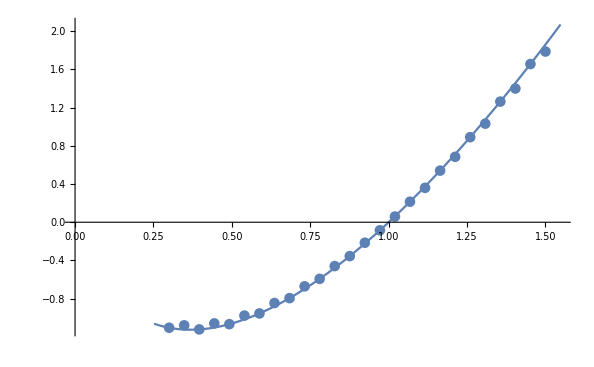

0.0733225

InterpolatingFunction[…]

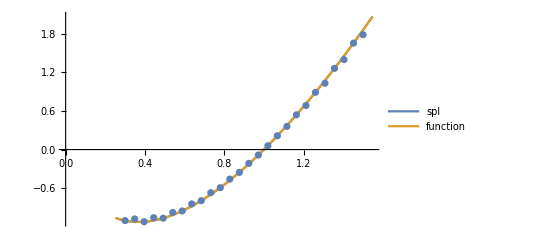

```mathematica
n=Length[arr1];funk1={};
For[i=1,i≤n,i+=2,funk1=Append[funk1,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk1]
inpln1:=InterpolatingPolynomial[funk1,x]
Collect[inpln1,x]
gr11:=Plot[inpln1,{x,0.252,1.548},AxesOrigin->{0,0}];
gr21:=ListPlot[funk];
Show[{gr11,gr21}]

g[x_]:=-0.02892690018160793-9.846764088904761 x+43.794182354191435 x^2-146.62318636895466 x^3+388.57319542465143 x^4-758.5707331668411 x^5+1084.1974546185008 x^6-1130.4680580940899 x^7+849.51780645953 x^8-447.82659506980724 x^9+157.07538399276922 x^10-32.9086974796021 x^11+3.114938356709965 x^12;
s=0;
For[i=1,i≤n,i++, p= Abs[g[arr1[[i]]]- arr2[[i]]];];
If[p>s,s=p,s=s];
s


sp1=Interpolation[funk1,Method->"Spline"]
gr31:=Plot[{inpln1,sp1[x]},{x,0.252,1.548},{PlotLegends->{ "spl","function"},AxesOrigin->{0,0}}];
gr21:=ListPlot[funk];
Show[{gr31,gr21}]
```

(0.3 | -1.10525
0.396 | -1.1225
0.54 | -0.978257
0.684 | -0.794931
0.828 | -0.459459
0.972 | -0.0844691
1.116 | 0.360097
1.26 | 0.891074
1.404 | 1.40065)

35.106-435.42 x+2186.67 x^2-6013.19 x^3+9932.53 x^4-10111.8 x^5+6215.22 x^6-2115.14 x^7+305.978 x^8

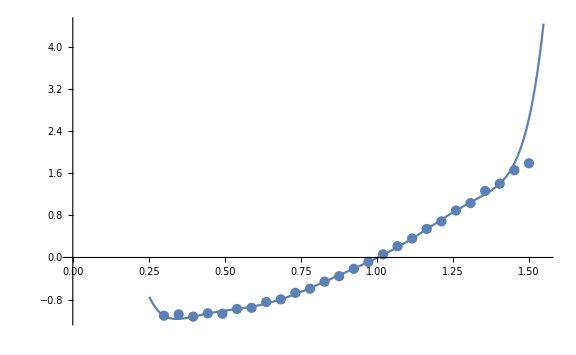

0.848223

InterpolatingFunction[…]

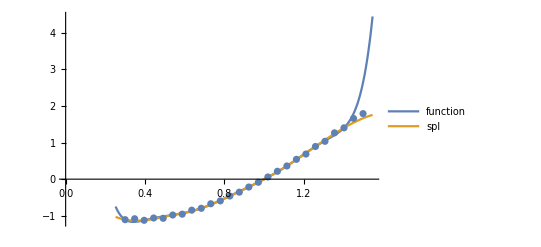

```mathematica
n=Length[arr1];funk2={{0.3,-1.10525}};

For[i=3,i≤n,i+=3,funk2=Append[funk2,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk2]
inpln2:=InterpolatingPolynomial[funk2,x]
Collect[inpln2,x]
gr12:=Plot[inpln2,{x,0.252,1.548},AxesOrigin->{0,0}];
gr22:=ListPlot[funk];
Show[{gr12,gr22}]

g[x_]:=35.10601276934891-435.4197394696434 x+2186.672711909068 x^2-6013.192423374079 x^3+9932.529838537586 x^4-10111.75694921752 x^5+6215.219355315923 x^6-2115.1439977643463 x^7+305.97786249055474 x^8;
s=0;
For[i=1,i≤n,i++, p= Abs[g[arr1[[i]]]- arr2[[i]]];];
If[p>s,s=p,s=s];
s



sp2=Interpolation[funk2,Method->"Spline"]
gr32:=Plot[{inpln2,sp2[x]},{x,0.252,1.548},{PlotLegends->{"function", "spl"},AxesOrigin->{0,0}}];
gr22:=ListPlot[funk];
Show[{gr32,gr22}]
```

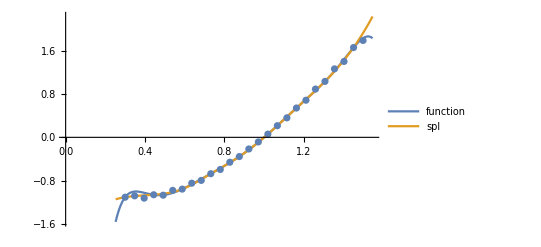

```mathematica
InterpolatingFunction[…]
```

(0.3 | -1.10525
0.492 | -1.06783
0.732 | -0.671395
0.972 | -0.0844691
1.212 | 0.685119
1.452 | 1.65703)

0.154418-8.77318 x+20.3785 x^2-20.0042 x^3+10.2847 x^4-2.04516 x^5

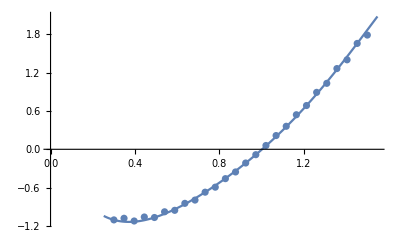

0.0797001

InterpolatingFunction[…]

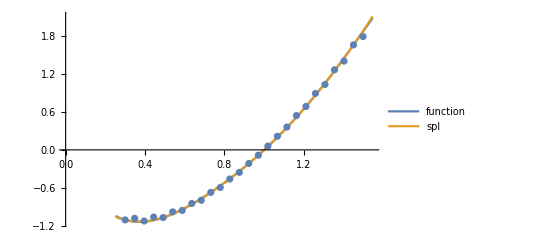

```mathematica
n=Length[arr1];funk3={{0.3,-1.10525}};
For[i=5,i≤n,i+=5,funk3=Append[funk3,{arr1[[i]],arr2[[i]]}]];
MatrixForm[funk3]
inpln3:=InterpolatingPolynomial[funk3,x]
Collect[inpln3,x]
gr13:=Plot[inpln3,{x,0.252,1.548},AxesOrigin->{0,0}];
gr23:=ListPlot[funk];
Show[{gr13,gr23}]
g[x_]:=0.15441832456109705-8.77318084192237 x+20.378486773302022 x^2-20.004226100727436 x^3+10.284685253923707 x^4-2.0451553163411123 x^5;
s=0;
For[i=1,i≤n,i++, p= Abs[g[arr1[[i]]]- arr2[[i]]];];
If[p>s,s=p,s=s];
s


sp3=Interpolation[funk3,Method->"Spline"]
gr33:=Plot[{inpln3,sp3[x]},{x,0.252,1.548},{PlotLegends->{"function", "spl"},AxesOrigin->{0,0}}];
gr23:=ListPlot[funk];
Show[{gr33,gr23}]
```